Approximate the force between the electromagnet and the permanent magnet with an approximation of the force between two single-loop coils

## Permanent Magnet Info

[Magnet Source](https://www.kjmagnetics.com/proddetail.asp?prod=DE3)

The units are REALLY funky but 13200 Gauss is the same as 13200 Oersted here.

```mathematica
magradius = Quantity[0.4375, "Inches"]
magheight = Quantity[0.1875, "Inches"]
magweight = Quantity[13.86, "Grams"]
magBrmax = Quantity[13200, "Oersteds"]
```

0.4375 in

0.1875 in

13.86 g

13200 Oe

```mathematica
Quantity[13200, "Gauss"]
```

calculate the “Magnetization” based on a formula from Rebecca Christianson.

```mathematica
magnetization = magBrmax/(4π)
```

3300/π Oe

```mathematica
UnitConvert[magnetization,"A/m"]
```

825000/π^2 A/m

Calculate current in a single-loop approximation of the permanent magnet

```mathematica
magI = UnitConvert[magnetization*magheight, "Amp"]
```

398.097 A

## Electromagnet Info

[Tentative Info](https://apwelectromagnets.com/em100-12-222.html?category_id=7#product-details-tab-specification)

From the website we know is that it has a pull force of 25 lb against a 0.25” thick steel plate, and that it has a diameter of 1 inch and a height of 0.78”. That’s not enough info though.

Here’s the data from the Hall probe at various currents. All are the maximum for the surface.

{0.3876,{1,0.2},{1.5,0.25},{2,0.4},{2.46,0.42},{3,0.45},{4.81,0.6}}

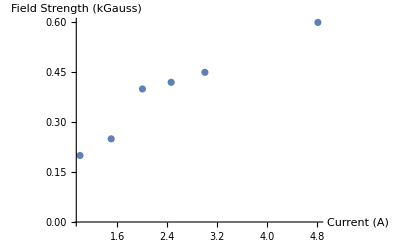

```mathematica
surfmag = {{0.5, 0.09}.{0.75, 0.14}, {1, 0.2}, { 1.5, 0.25}, { 2, 0.4}, {2.46, 0.42}, {3, 0.45}, {4.81, 0.6}}
ListPlot[surfmag, AxesLabel->{"Current (A)", "Field Strength (kGauss)"}]
```

this is not pretty. oh well. The saturation current is supposed to be around 1.5A, so the electromagnet gets hot very quickly beyond that. let’s use the 1.5A, 0.25 kG measurement
This converts to 19942.5 A/m

everything below this is old

```mathematica
mag2height = Quantity[0.25, "Inches"]
```

0.25 in

```mathematica
magI2 = UnitConvert[magnetization*mag2height, "Amp"]
```

530.796 A

if we divide this by the actual current required to provide the force, 0.33A, we get the theoretical number of coils:

```mathematica
emCoils = magI2/Quantity[0.33, "Amperes"]
```

1608.47

that' s a lot of coils but okay

## Function to calculate the force

Magnetic field along the central axis as a function only of distance from the magnet:
e is permeability of free space. It was causing unit problems so I got rid of all units (assuming MKS). Its units are (m kg)/(s^2 A^2)

```mathematica
e = 1.3 * 10^-6
```

1.3×10^-6

```mathematica
m1 = e/2 QuantityMagnitude[magI]
m2 = e/2 QuantityMagnitude[magI2]
```

0.000258763

0.000345018

function to determine shape

```mathematica
b[m_, r_, z_] := (m r^2)/((r^2 + z^2)^(3/2))
```

```mathematica
bSum[gap_,h_] := b[m1, 0.0127 , h]+b[m2, 0.0127, gap - h]
```

```mathematica
(bSum[gap, h])^2
```

((5.56479×10^-8)/((0.00016129+(gap-h)^2)^(3/2))+(4.17359×10^-8)/((0.00016129+h^2)^(3/2)))^2

```mathematica
eGap[gap_, h_] := ((5.5647893224005975*^-8)/((0.00016129+(gap-h)^2)^(3/2))+(4.1735919918004476*^-8)/((0.00016129+h^2)^(3/2)))^2
```

```mathematica
F[gap_] := Derivative[1,0][∫_0^gap eGap[gap, h]ⅆh]
```

This doesn' t want to calculate so let’s approximate with a sum? No, wait, it needs to be derivativeified.

```mathematica
∫_0^s π(.005)^2(bSum[0.01, z])^2 ⅆz
```

∫_0^s ((5.56479×10^-8)/((0.00016129+(0.01-z)^2)^(3/2))+(4.17359×10^-8)/((0.00016129+z^2)^(3/2)))^2 ⅆz

```mathematica
Simplify[∫_0^0.01 (bSum[0.01, z])^2 ⅆz]
```

$Aborted

```mathematica
∫_0^0.01 eGap[0.01, h]ⅆh
```

$Aborted

```mathematica
Simplify[eGap[a, b]]
```

((5.56479×10^-8)/((0.00016129+(a-b)^2)^(3/2))+(4.17359×10^-8)/((0.00016129+b^2)^(3/2)))^2